```mathematica
ω[z_,c_]:=z+c⟦1⟧/z+ c⟦2⟧/z^2+ c⟦3⟧/z^3;
dω[z_,c_]:=1-c⟦1⟧/z^2-2 c⟦2⟧/z^3-3 c⟦3⟧/z^4;
φ0[z_,a_]:=a⟦1⟧/z+a⟦2⟧/z^2+a⟦3⟧/z^3;
dφ0[z_,a_]:=-a⟦1⟧/z^2-2 a⟦2⟧/z^3-3 a⟦3⟧/z^4;
ϕ0[z_,a_,c_]:=dφ0[z,a]/dω[z,c];
ϕ[z_,a_,c_]:=(1/4+dφ0[z,a])/dω[z,c];
Q[z_,q_]:=q⟦1⟧+q⟦2⟧*z+q⟦3⟧*z^2+q⟦4⟧*z^3;
Kk[z_,k_]:=Conjugate[k⟦1⟧]/z+Conjugate[k⟦2⟧]/z^2+Conjugate[k⟦3⟧]/z^3;
ψ0[z_,a_,c_,q_,k_]:=-1/(4 z)-Conjugate[Q[z,q]]ϕ[z,a,c]-Kk[z,k]; 

sω[z_]:=1/z-1/6 z^3;
sφ0[z_]:=3/7 z+z^3/12;
sψ0[z_]:=-1/12(z^3+(13 z-26*3/7*z^3)/(z^4+2)); (* tukaj sem nastavil po Savinu celotni funkciji, ne samo 0!! *)
```

```mathematica
c={0,0,-1/6};
p={0,0,-1/6};
q={0,13/12,0,0};
a={3/7,0,1/24} ; 
k={1/48,0,0};
(*
c//N
p//N
q//N
a//N
k//N
*)

Γ1=1/4;
Γ2=-1/2;

φ[z_,c_,a_]:=Γ1 z+φ0[z,a];
ψ[z_,a_,c_,q_,k_]:=Γ2 z+ψ0[z,a,c,q,k];

sφ[z_]:=1/4 sω[z]+sφ0[z];
sψ[z_]:=-1/2 sω[z]+sψ0[z];

(* function derivation *)
```

```mathematica
S=1000;
aa=Table[N[i/S*π/2],{i,0,S}];
rr=1.1;
```

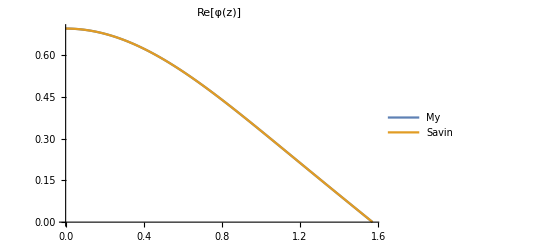

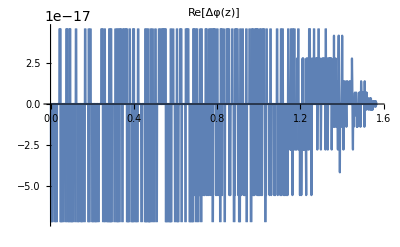

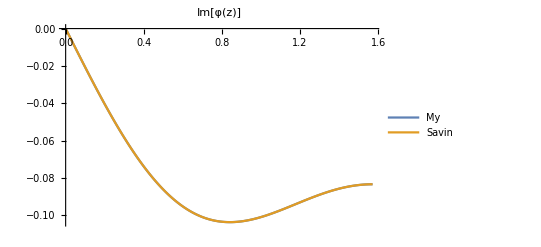

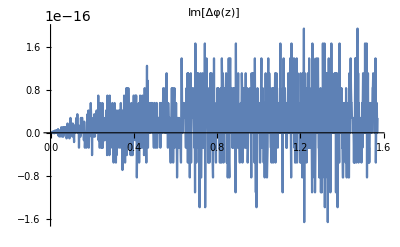

```mathematica
mPhi=φ[z,c,a];
sPhi=sφ[z];

sMyPhiData={#,Re[mPhi/.z->rr*Exp[ⅈ #]]}&/@aa;
sSavinPhiData={#,Re[sPhi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[{sMyPhiData,sSavinPhiData},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"Re[φ(z)]"]
deltaPhiData={#,Re[mPhi/.z->rr*Exp[ⅈ #]]-Re[sPhi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[deltaPhiData,Joined->True,PlotLabel->"Re[Δφ(z)]"]

sMyPhiData={#,Im[mPhi/.z->rr*Exp[ⅈ #]]}&/@aa;
sSavinPhiData={#,Im[sPhi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[{sMyPhiData,sSavinPhiData},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"Im[φ(z)]"]
deltaPhiData={#,Im[mPhi/.z->rr*Exp[ⅈ #]]-Im[sPhi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[deltaPhiData,Joined->True,PlotLabel->"Im[Δφ(z)]"]
```

(36 z-91 z^3-84 z^5)/(84+168 z^4)

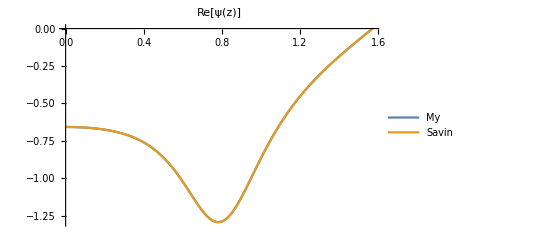

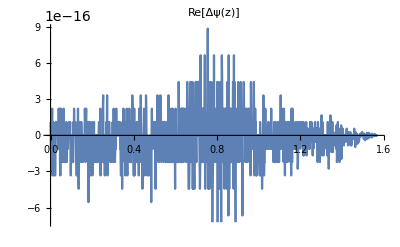

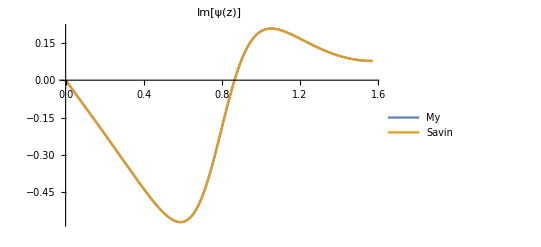

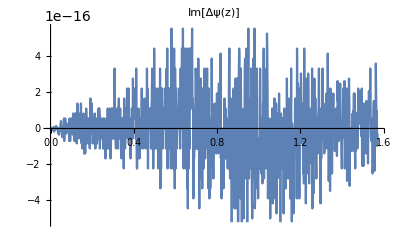

```mathematica
psi=Γ2*z-Γ1/z-ϕ[z,a,c]*u[z] -1/(48*z);
mPsi=psi/.u[z]->13/12*1/z//Simplify
sPsi=sψ[z];

sMyPsiData={#,Re[mPsi/.z->rr*Exp[ⅈ #]]}&/@aa;
sSavinPsiData={#,Re[sPsi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[{sMyPsiData,sSavinPsiData},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"Re[ψ(z)]"]
deltaPsiData={#,Re[mPsi/.z->rr*Exp[ⅈ #]]-Re[sPsi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[deltaPsiData,Joined->True,PlotLabel->"Re[Δψ(z)]"]

sMyPsiData={#,Im[mPsi/.z->rr*Exp[ⅈ #]]}&/@aa;
sSavinPsiData={#,Im[sPsi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[{sMyPsiData,sSavinPsiData},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"Im[ψ(z)]"]
deltaPsiData={#,Im[mPsi/.z->rr*Exp[ⅈ #]]-Im[sPsi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[deltaPsiData,Joined->True,PlotLabel->"Im[Δψ(z)]"]
```

(4 z (-3+7 z^2+6 z^4))/(7 (1+2 z^4)^2)

-1/2+13/(48 z^2)-((-7-24 z^2+14 z^4) du[z])/(28+56 z^4)-(4 z (-3+7 z^2+6 z^4) u[z])/(7 (1+2 z^4)^2)

(36-273 z^2-636 z^4+182 z^6-168 z^8)/(84 (1+2 z^4)^2)

-13/(48 z)-(13 (1/4-1/(8 z^4)-3/(7 z^2)))/(12 (1+1/(2 z^4)) z)-z/2

(36-273 z^2-636 z^4+182 z^6-168 z^8)/(84 (1+2 z^4)^2)

(36-273 z^2-636 z^4+182 z^6-168 z^8)/(84 (1+2 z^4)^2)

(36-273 z^2-636 z^4+182 z^6-168 z^8)/(84 (1+2 z^4)^2)

(168-182 z^2+636 z^4+273 z^6-36 z^8)/(84 z^2 (2+z^4)^2)

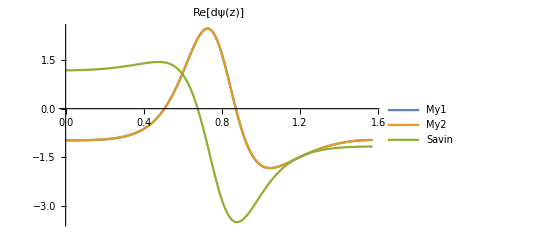

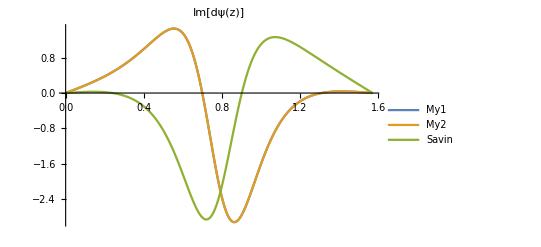

```mathematica
pphi=ϕ[z,a,c];
Dpphi=D[pphi,z]//Simplify
dpsi=Γ2+Γ1/z^2-Dpphi*u[z]-pphi*du[z] +1/(48*z^2);
dpsi//Simplify
dpsi1=dpsi/.{u[z]->13/12*1/z,du[z]->-13/12*1/z^2}//Simplify

tpsi=psi/.u[z]->13/12*1/z
dpsi2=D[tpsi,z]//Simplify
mDPsi1=dpsi1
mDPsi2=dpsi2


sDPsi=D[sPsi,z]//Simplify

sMyPsi1Data={#,Re[mDPsi1/.z->rr*Exp[ⅈ #]]}&/@aa;
sMyPsi2Data={#,Re[mDPsi2/.z->rr*Exp[ⅈ #]]}&/@aa;
sSavinPsiData={#,Re[sDPsi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[{sMyPsi1Data,sMyPsi2Data,sSavinPsiData},Joined->True,PlotLegends->LineLegend[{"My1","My2","Savin"}],PlotLabel->"Re[dψ(z)]",PlotRange->All]

sMyPsi1Data={#,Im[mDPsi1/.z->rr*Exp[ⅈ #]]}&/@aa;
sMyPsi2Data={#,Im[mDPsi2/.z->rr*Exp[ⅈ #]]}&/@aa;
sSavinPsiData={#,Im[sDPsi/.z->1/rr*Exp[-ⅈ #]]}&/@aa;
ListPlot[{sMyPsi1Data,sMyPsi2Data,sSavinPsiData},Joined->True,PlotLegends->LineLegend[{"My1","My2","Savin"}],PlotLabel->"Im[dψ(z)]",PlotRange->All]
```

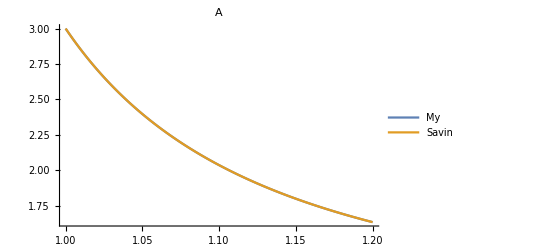

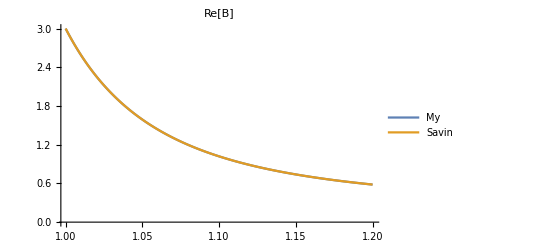

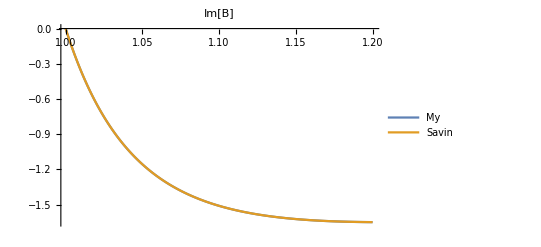

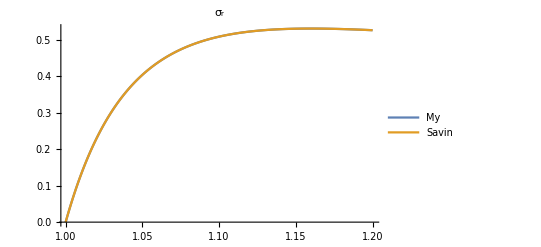

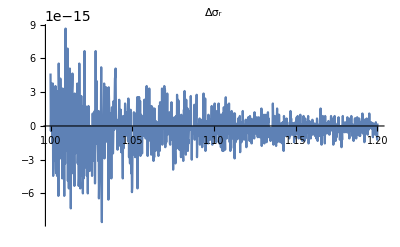

σ_φ(0)=3.

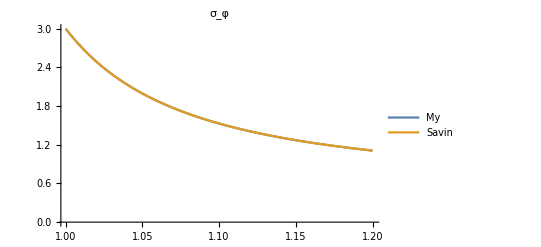

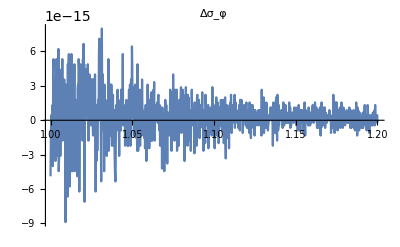

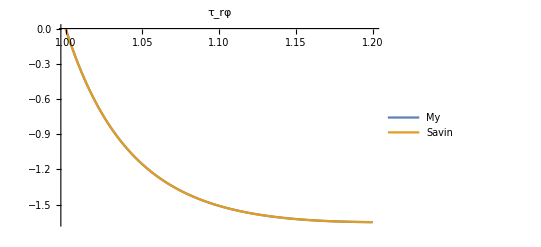

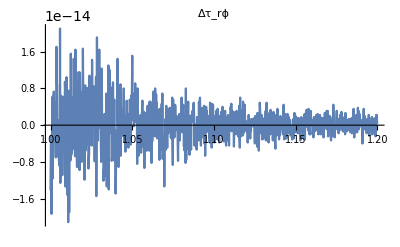

```mathematica
S=1000;
ρ=Table[N[(1+0.2*i/S)*Exp[ⅈ π/4]],{i,0,S}];
w=ω[z,c];
dw=D[w,z];
ddw=D[dw,z];

sw=sω[z];
dsw=D[sw,z];
ddsw=D[dsw,z];
spphi=D[sPhi,z]/dsw;
Dspphi=D[spphi,z];

A=4*Re[pphi]/.z->#&/@ρ;
B=2*z^2/(Abs[z]^2*Conjugate[dw])*(Conjugate[w]*Dpphi+mDPsi1)/.z->#&/@ρ;

sA=4*Re[spphi]/.z->1/#&/@ρ;
sB=2*z^2/(Abs[z]^2*Conjugate[dsw])*(Conjugate[sw]*Dspphi+sDPsi)/.z->1/#&/@ρ;

σr=(A-Re[B])/2;
σf=(A+Re[B])/2;
τ=Im[B];

sσr=(sA-Re[sB])/2;
sσf=(sA+Re[sB])/2;
sτ=Im[sB];

ρ=Abs[ρ];

ListPlot[{Transpose[{ρ,A}],Transpose[{ρ,sA}]},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"A"]
ListPlot[{Transpose[{ρ,Re[B]}],Transpose[{ρ,Re[sB]}]},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"Re[B]"]
ListPlot[{Transpose[{ρ,Im[B]}],Transpose[{ρ,Im[sB]}]},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"Im[B]"]


ListPlot[{Transpose[{ρ,σr}],Transpose[{ρ,sσr}]},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"σ_r"]
ListPlot[Transpose[{ρ,σr-sσr}],Joined->True,PlotLabel->"Δσ_r",PlotRange->All]
Print["σ_φ(0)=",σf⟦1⟧];
ListPlot[{Transpose[{ρ,σf}],Transpose[{ρ,sσf}]},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"σ_φ"]
ListPlot[Transpose[{ρ,σf-sσf}],Joined->True,PlotLabel->"Δσ_φ",PlotRange->All]
ListPlot[{Transpose[{ρ,τ}],Transpose[{ρ,sτ}]},Joined->True,PlotLegends->LineLegend[{"My","Savin"}],PlotLabel->"τ_rφ"]
ListPlot[Transpose[{ρ,τ-sτ}],Joined->True,PlotLabel->"Δτ_rϕ",PlotRange->All]
```